```mathematica
SetDirectory["/Users/lrf/Dropbox/bloch"]
```

/Users/lrf/Dropbox/bloch

{3200}

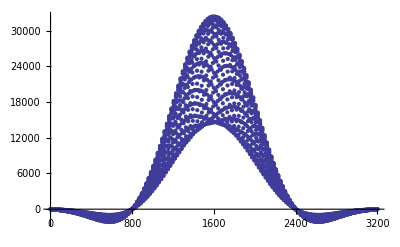

```mathematica
rfsinc=BinaryReadList["msrf2_sinc.rho","Integer32"];
Dimensions[rfsinc]
ListPlot[rfsinc,PlotRange->All]
```

{3200}

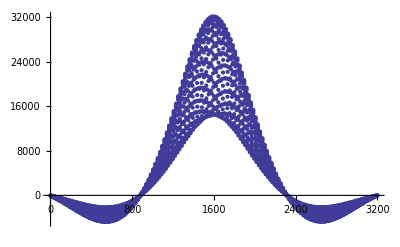

```mathematica
rfslr=BinaryReadList["msrf2_slr.rho","Integer32"];
Dimensions[rfslr]
ListPlot[rfslr,PlotRange->All]
```

```mathematica
f=ListInterpolation[rfslr]
```

InterpolatingFunction[{{1,400}},<>]

{3200}

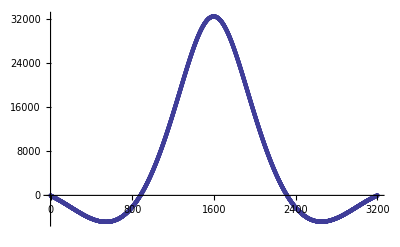

```mathematica
rfslrInterp=Table[Round[f[x]],{x,1,400,399/3199}];
Dimensions[rfslrInterp]
ListPlot[rfslrInterp]
```

```mathematica
BinaryWrite["/Users/lrf/Dropbox/bloch/msrf2_slr3200.rho",rfslrInterp,"Integer16"]
```

/Users/lrf/Dropbox/bloch/msrf2_slr3200.rho

{3200}

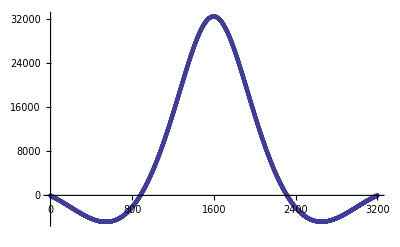

```mathematica
rfslr=BinaryReadList["msrf2_slr3200.rho","Integer16"];
Dimensions[rfslr]
ListPlot[rfslr,PlotRange->All]
```

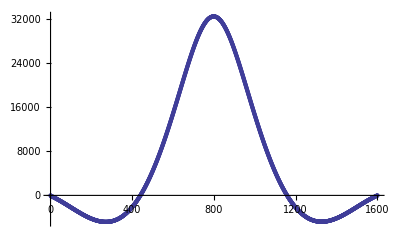

```mathematica
rfslr1600=Table[rfslr[[i]],{i,1,Length[rfslr],2}];
ListPlot[rfslr1600,PlotRange->All]
```

```mathematica
BinaryWrite["/Users/lrf/Dropbox/bloch/msrf2_slr1600.rho",rfslr1600,"Integer16"]
```

/Users/lrf/Dropbox/bloch/msrf2_slr1600.rho

```mathematica
rfslr1600
```

{-1507328,-6357074,-9699466,-12058801,-14155984,-16646389,-19136795,-21627201,-24117607,-26608013,-29098419,-31654362,-34210305,-36831785,-39453265,-42009208,-44696225,-47448778,-50201332,-52822813,-55575366,-58393457,-61146012,-63898566,-66716656,-69534747,-72418375,-75302003,-78185631,-81069259,-83952887,-86902052,-89851217,-92734845,-95618473,-98633174,-101647876,-104597041,-107546206,-110495372,-113510074,-116524776,-119539478,-122554180,-125568882,-128583583,-131598285,-134678524,-137758763,-140773465,-143722631,-146737333,-149752035,-152832274,-155912512,-158861678,-161810842,-164891081,-167971320,-170920485,-173804114,-176818816,-179833518,-182717146,-185600774,-188549939,-191499104,-194382732,-197200823,-200084451,-202968079,-205851707,-208735335,-211487889,-214240443,-217058534,-219811089,-222563642,-225185123,-227872140,-230559157,-233246174,-235933191,-238423597,-240914003,-243469946,-245960353,-248385222,-250810091,-253234960,-255659829,-258019161,-260378493,-262541215,-264638399,-266866657,-269094915,-271323172,-273420357,-275386468,-277352578,-279318688,-281284797,-283119834,-284954870,-286658832,-288297258,-290066756,-291705182,-293343607,-294850958,-296423846,-297865661,-299307474,-300618215,-301797882,-302977548,-304157214,-305336879,-306385472,-307434064,-308351583,-309269100,-310055545,-310841989,-311497360,-312152729,-312677026,-313201322,-313660082,-314118840,-314380989,-314512063,-314643138,-314774212,-314774212,-314774212,-314708675,-314512065,-314315454,-313987770,-313594548,-313070252,-312545956,-311956123,-311169680,-310383236,-309531255,-308548201,-307565146,-306451018,-305271352,-304026149,-302649873,-301273595,-299766245,-298127821,-296423859,-294654360,-292688251,-290722141,-288756030,-286658847,-284496126,-282136795,-279711926,-277155984,-274665578,-272109635,-269291545,-266407917,-263458752,-260509587,-257298276,-254021425,-250679039,-247336652,-243797655,-240193120,-236457511,-232656365,-228724146,-224660853,-220597559,-216468728,-212143287,-207752308,-203164719,-198511592,-193792928,-189074264,-184224527,-179178179,-174066292,-168757796,-163449300,-158075266,-152504621,-146737366,-140970110,-135137317,-129173451,-123144047,-116983570,-110757555,-104400466,-97846767,-91227531,-84542757,-77792446,-70845525,-63833066,-56689533,-49414927,-42074783,-34603566,-27066811,-19333446,-11534543,-3866713,3801116,11862166,20185364,28574100,37028372,45482646,54067993,62915486,71828518,80741550,89851192,99026372,108463699,117901027,127469429,137168904,146933916,156764467,166726090,176884324,187108096,197331868,207686714,218238170,228920700,239734305,250613446,261492589,272502804,283709630,295047531,306516505,318051016,329585529,341251114,353047774,364975507,377034315,389224196,401479615,413800570,426187064,438770167,451484344,464264059,477043774,489954563,502996425,516169361,529407835,542777383,556212467,569647553,583279248,597042017,610870324,624698631,638723548,652748467,666969995,681191524,695544126,709962266,724445943,739060693,753675444,768421269,783232630,798175066,813117502,828191012,843330058,858469105,873739226,889074883,904410541,919877273,935344005,950810737,966408543,982137422,997866302,1013660719,1029389599,1045184015,1061043969,1076969460,1092894952,1108820442,1124811469,1140868035,1156924600,1172981165,1189037729,1205094295,1221216397,1237404035,1253526137,1269582703,1285704804,1301761370,1317817935,1333874499,1349865528,1365922093,1381847584,1397707539,1413633029,1429492984,1445352938,1461081818,1476810698,1492408505,1508006311,1523604117,1539005313,1554209897,1569480017,1584684602,1599823650,1614831623,1629577449,1644257737,1658806952,1673356166,1687774306,1701995836,1716086292,1730045673,1743808444,1757505677,1771006300,1784244775,1797352176,1810328502,1823108217,1835625786,1848012279,1860202162,1872195433,1883926558,1895526607,1906864509,1917940263,1928819406,1939436400,1949725711,1959883946,1969780034,1979348438,1988654693,1997698800,2006480759,2015000570,2023258233,2031188212,2038790505,2046130650,2053208647,2060024496,2066447123,2072542065,2078309323,2083814431,2088926319,2093710521,2098167039,2102361408,2106293628,2109767092,2112912868,2115730960,2118221368,2120384090,2122219127,2123660943,2124709537,2125495981,2125954741,2126020280,2125692597,2125102765,2124185248,2122874510,2121236086,2119204440,2116910647,2114289167,2111274467,2107866545,2104196474,2100198718,2095873277,2091220151,2086173803,2080734234,2075032516,2069068650,2062711563,2056157864,2049342017,2042198485,2034661731,2026862829,2018801779,2010413045,2001696625,1992783593,1983608414,1974105551,1964406075,1954378915,1944155144,1933669225,1922855621,1911845406,1900704117,1889300680,1877635095,1865772899,1853714092,1841458673,1828941107,1816226930,1803447215,1790405353,1777166879,1763731796,1750165637,1736468404,1722574561,1708549643,1694393652,1680041050,1665557373,1650942623,1636327872,1621647584,1606770685,1591762713,1576558130,1561353546,1545952352,1530551157,1515149962,1499683230,1484085424,1468422081,1452693202,1436964322,1421104368,1405178877,1389187850,1373262359,1357271331,1341345840,1325289275,1309232711,1293176145,1277054044,1260997478,1244940913,1228818811,1212762246,1196640144,1180583579,1164527015,1148535986,1132413884,1116357319,1100497364,1084571874,1068646383,1052720891,1036860937,1021066520,1005337640,989674297,973945417,958282074,942815341,927348609,911881877,896480682,881079487,865743829,850670317,835596807,820523297,805515324,790572888,775695989,760884626,746204338,731655123,717171446,702687769,688269629,673982562,659761033,645670578,631711196,617751815,603857971,590095200,576397967,562831807,549331185,536092711,522919774,509746837,496704972,483663110,470817857,457907068,445192889,432544248,420092217,407771260,395515841,383391496,371332688,359404953,347542756,335811632,324146046,312480461,301011485,289673583,278532292,267391003,256446322,245567181,234884648,224136581,213519587,203099203,192744356,182520584,172362348,162400724,152504636,142608550,132843536,123340670,113903342,104531550,95225296,86115653,77137083,68224051,59376556,50594598,42009249,33554976,25231777,16908578,8781989,917548,-6750283,-14549185,-22282552,-29884844,-37356063,-44761744,-52036351,-59114348,-66126808,-73139266,-80020652,-86770963,-93390201,-99878364,-106300991,-112658080,-118884095,-124979037,-130942904,-136841235,-142739564,-148441284,-153946393,-159385965,-164694462,-170002959,-175180383,-180226732,-185142007,-190057282,-194841484,-199494611,-204016665,-208407644,-212667550,-216992991,-221187360,-225185118,-229051801,-232918484,-236654094,-240324166,-243863165,-247336626,-250679014,-253955864,-257101640,-260181880,-263131045,-266080210,-268963838,-271716392,-274337873,-276828279,-279187612,-281546944,-283775203,-285937924,-288035108,-289935682,-291836255,-293671291,-295375254,-297013679,-298521031,-299962845,-301339122,-302584326,-303829528,-305009194,-306057787,-307040843,-307958360,-308744805,-309531249,-310252156,-310841990,-311366287,-311825045,-312152731,-312349343,-312611490,-312808101,-312873639,-312808102,-312742565,-312611491,-312349344,-312087196,-311759511,-311300753,-310841994,-310317698,-309727865,-309006959,-308286052,-307499608,-306647627,-305664573,-304747055,-303764000,-302715408,-301535743,-300356077,-299110874,-297800134,-296358321,-294982043,-293540229,-292032878,-290394454,-288821566,-287183141,-285479179,-283644144,-281874645,-280039609,-278073500,-276107390,-274206816,-272240706,-270143523,-268046339,-265949155,-263786434,-261558177,-259329919,-257101660,-254807865,-252382998,-249958129,-247533260,-245108391,-242683521,-240193115,-237637173,-235081230,-232525287,-229903807,-227216791,-224529774,-221842757,-219221276,-216468722,-213716169,-210963615,-208211061,-205392970,-202509342,-199691250,-196873160,-194055068,-191171441,-188222276,-185273111,-182389483,-179505855,-176556690,-173541988,-170527287,-167643658,-164628957,-161614255,-158665089,-155715924,-152701223,-149620984,-146606281,-143657117,-140642415,-137562176,-134613010,-131663845,-128649143,-125568905,-122488666,-119473964,-116524798,-113575634,-110626468,-107611766,-104597065,-101713436,-98764271,-95815106,-92931478,-90047850,-87098685,-84149521,-81265892,-78382264,-75498636,-72615008,-69796917,-66978826,-64226271,-61473717,-58655627,-55837536,-53084982,-50463501,-47776484,-45089467,-42402450,-39780970,-37225027,-34603547,-31982067,-29426124,-26935717,-24445312,-21954906,-19464500,-17039630,-14614761,-12255429,-9961634,-7667839,-5242970,-3014711,-917526}